(ⅇ^x+y)/(ⅇ^y+x)

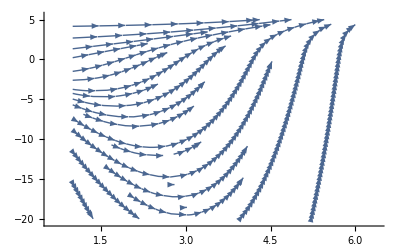

```mathematica
f[x_,y_] = (y+E^x)/(x+E^y)
StreamPlot[{1,f[x,y]},{x,1,6},{y,-20,5},Frame->False,Axes->True,AspectRatio->1/GoldenRatio]
```

```mathematica
f[x_,y_,z_] = {0.8*x-y,x-z,y^3-1*z}
v = VectorPlot3D[f[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2}]
```

{0.8 x-y,x-z,y^3-z}

```mathematica
f1[x_,y_] = 0.8*x-y;
f2[x_,z_] = x-z;
f3[y_,z_]= y^3-1*z;
StreamPlot[
```

```mathematica
f[x_,y_,z_] = {0.8*x-y,x-z,y^3-1*z};
f1[x_,y_] = 0.8*x-y;
f2[x_,z_] = x-z;
f3[y_,z_]= y^3-1*z;
c1 = ContourPlot3D[f1[x,y,z]==0,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Scientific"];
c2 = ContourPlot3D[f2[x,y,z]==0,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Detailed"];
c3 = ContourPlot3D[f3[x,y,z]==0,{x,-2,2},{y,-2,2},{z,-2,2},MeshFunctions-> (Norm[{#1,#2,#3}]&),MeshShading->{None},ContourStyle->{Directive[Orange,Opacity[0.8]]}];
Show[c1,c2,c3]

c = ContourPlot3D[f[x,y,z]==0,{x,-2,2},{y,-2,2},{z,-2,2},PlotTheme->"Minimal",Lighting-> "Neutral",AxesEdge->{{-2,2},{-2,2},{-2,2}},AxesLabel->{x,y,z}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[v,c]
```

-Graphics3D-

```mathematica
S=2;
test=StreamPlot[{x-S,2 x*y-S},{x,0,3},{y,0,3}];
Make3d[plot_,height_]:=N@First@Graphics@plot/.{skip:_Arrowheads:>skip,{x_?AtomQ,y_?AtomQ}:>{height,x,y}}
Show[Graphics3D[Make3d[test,0]],Axes->True]
```

-Graphics3D-

```mathematica
fieldSolve[field_,varlist_,xi0_,tmax_,debug_: False]:=Module[{xiVec,equationSet,t},If[Length[varlist]≠Length[xi0],Print["Number of variables must equal number of initial conditions\nUSAGE:\n"<>fieldSolve::usage];Abort[]];
xiVec=Through[varlist[t]];
(*Below,Simplify[equationSet] would cost extra time and doesn't help with the numerical solution,so don't try to simplify.*)equationSet=Join[Thread[Map[D[#,t]&,xiVec]==Normalize[field/.Thread[varlist->xiVec]]],Thread[(xiVec/.t->0)==xi0]];
If[debug,Print[Row[{"Numerically solving the system of equations\n\n",TraditionalForm[(Simplify[equationSet]/.t->"t")//TableForm]}]]];
(*This is where the differential equation is solved.The Quiet[] command suppresses warning messages because numerical precision isn't crucial for our plotting purposes:*)Map[Head,First[xiVec/.Quiet[NDSolve[equationSet,xiVec,{t,0,tmax}]]],2]]

fieldLinePlot[field_,varList_,seedList_,opts:OptionsPattern[]]:=Module[{sols,localVars,var,localField,plotOptions,tubeFunction,tubePlotStyle,postProcess={}},plotOptions=FilterRules[{opts},Options[ParametricPlot3D]];
tubeFunction=OptionValue["TubeFunction"];
If[tubeFunction=!=None,tubePlotStyle=Cases[OptionValue[PlotStyle],Except[_Tube]];
plotOptions=FilterRules[plotOptions,Except[{PlotStyle,ColorFunction,ColorFunctionScaling}]];
postProcess=Line[x_]:>Join[tubePlotStyle,{CapForm["Butt"],Tube[x,tubeFunction@@@x]}]];
If[Length[seedList[[1,1]]]≠Length[varList],Print["Number of variables must equal number of initial conditions\nUSAGE:\n"<>fieldLinePlot::usage];Abort[]];
localVars=Array[var,Length[varList]];
localField=ReleaseHold[Hold[field]/.Thread[Map[HoldPattern,Unevaluated[varList]]->localVars]];
(*Assume that each element of seedList specifies a point AND the length of the field line:*)Show[ParallelTable[ParametricPlot3D[Evaluate[Through[#[t]]],{t,#[[1,1,1,1]],#[[1,1,1,2]]},Evaluate@Apply[Sequence,plotOptions]]&[fieldSolve[localField,localVars,seedList[[i,1]],seedList[[i,2]]]]/.postProcess,{i,Length[seedList]}]]];

Options[fieldLinePlot]=Append[Options[ParametricPlot3D],"TubeFunction"->None];

SyntaxInformation[fieldLinePlot]={"LocalVariables"->{"Solve",{2,2}},"ArgumentsPattern"->{_,_,_,OptionsPattern[]}};

SetAttributes[fieldSolve,HoldAll];

f2[x_,y_,z_]:={x,y,z}/Norm[{x,y,z}]^3-({x,y,z}-{1,1,1})/Norm[{x,y,z}-{1,1,1}]^3

f[x_,y_,z_] := {0.8*x-y,x-z,y^3-1*z}

seedList=Flatten[Table[{{x,y,z},200},{x,-2,2,.5},{y,-2,2,.5},{z,-2,2,.5}],2];

Show[fieldLinePlot[f[x,y,z],{x,y,z},seedList,PlotStyle->{Orange,Specularity[White,16]},PlotRange->All,Boxed->False]]
```

```mathematica
ClearAll
ClearAttributes
ClearSystemCache
a = 0.8;c =1;
f1[t_,y_] = 0.8*t-y;
f2[t_,z_] = t-z;
f3[y_,z_]= y^3-1*z;
f[t_,y_,z_] = {0.8*t-y,t-z,y^3-1*z};

ContourPlot3D[f[x,y,z]==0,{x,-2,2},{y,-2,2},{z,-2,2}]
(*cc1= ContourPlot[f1[x,y]==0,{x,-2,2},{y,-2,2}];
cc2 = ContourPlot[f2[y,z]==0,{y,-2,2},{z,-2,2}];
Make3d[plot_,height_]:=N@First@Graphics@plot/.{skip:_Arrowheads:>skip,{x_?AtomQ,y_?AtomQ}:>{height,x,y}};
pp1 = Table[Graphics3D[Make3d[cc1,i]],{i,-2,2}];
pp2 = Table[Make3d[cc2,i],{i,-2,2}];
Show[{pp1},Axes->True]
Rotate[Show[{pp1},Axes->True],90Degree]
Rotate[Show[{pp1},Axes->True],RotationTransform[pi/2,{{1,0,0},{0,1,0}}]]*)





(*S=2;
test=StreamPlot[{x-S,2 x*y-S},{x,0,3},{y,0,3}];*)
(*Make3d[plot_,height_]:=N@First@Graphics@plot/.{skip:_Arrowheads:>skip,{x_?AtomQ,y_?AtomQ}:>{height,x,y}}
Show[Graphics3D[Make3d[test,0]],Axes->True]*)


(*cc1=ContourPlot[f1[x,y]==0,{x,-2,2},{y,-2,2},AxesLabel->{x,y}]
Clear[z]
y = Table[y,{y,-2,2,0.5}];
cc2=ContourPlot[f2[x,z]==0,{x,-2,2},{z,-2,2}]*)
(*cc3=ContourPlot[f3[y,z]==0,{y,-2,2},{z,-2,2}]*)
(*ContourPlot3D[{f1[x,y]==0,f2[x,y]==0,f3[x,y]==0},{x,-2,2},{y,-2,2},{z,-2,2}]
ContourPlot3D[f[x,y,z]==0,{x,-2,2},{y,-2,2},{z,-2,2},AxesLabel->{x,y,z}]*)
```

ClearAll

ClearAttributes

ClearSystemCache

-Graphics3D-